## Convert data from hat.tile

```mathematica
r3 = Sqrt[3];
```

```mathematica
bases =<|6-> {{r3/2, -1/2},{r3/2, 1/2}},4->{{r3/4,-1/4},{r3/4,1/4}},3->{{1/r3,0},{1/2/r3,1/2}}|>
```

<|6→{{(√3)/2,-1/2},{(√3)/2,1/2}},4→{{(√3)/4,-1/4},{(√3)/4,1/4}},3→{{1/(√3),0},{1/(2 √3),1/2}}|>

```mathematica
hatTile = {
{6, 0, 0},
{4,-1, 0},
{3,-1, 0},
{4,-1,-1},
{6, 0,-1},
{4, 0,-3},
{3,-1,-2},
{4, 1,-3},
{3, 0,-2},
{4, 1,-2},
{6, 1,-1},
{4, 2,-1},
{3, 1,-1},
{4, 1,-1}
}
```

{{6,0,0},{4,-1,0},{3,-1,0},{4,-1,-1},{6,0,-1},{4,0,-3},{3,-1,-2},{4,1,-3},{3,0,-2},{4,1,-2},{6,1,-1},{4,2,-1},{3,1,-1},{4,1,-1}}

```mathematica
hat = Polygon[bases[#[[1]]]ᵀ.{#[[2]],#[[3]]}&/@hatTile]
```

Polygon[…]

```mathematica
bases[#[[1]]]ᵀ.{#[[2]],#[[3]]}&/@hatTile
```

{{0,0},{-(√3)/4,1/4},{-1/(√3),0},{-(√3)/2,0},{-(√3)/2,-1/2},{-(3 √3)/4,-3/4},{-2/(√3),-1},{-(√3)/2,-1},{-1/(√3),-1},{-(√3)/4,-3/4},{0,-1},{(√3)/4,-3/4},{1/(2 √3),-1/2},{0,-1/2}}

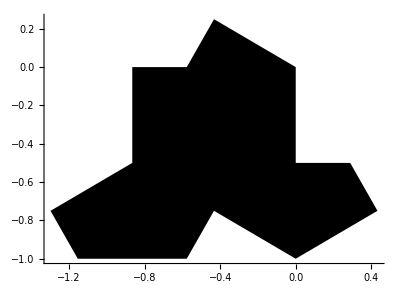

```mathematica
Graphics[hat, Axes->True]
```